```mathematica
Q1=λ1^2+λ2^2+λ3^2;
Q2=ArcCos[λ3/Sqrt[λ1^2+λ2^2+λ3^2]];
```

```mathematica
Clear[V]
```

```mathematica
V[λ1_,λ2_,λ3_]:={{2 λ1,2 λ2, 2 λ3},{(λ1 λ3)/((λ1^2+λ2^2+λ3^2)^(3/2) √(1-λ3^2/(λ1^2+λ2^2+λ3^2))),(λ2 λ3)/((λ1^2+λ2^2+λ3^2)^(3/2) √(1-λ3^2/(λ1^2+λ2^2+λ3^2))),-(-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2)))/(√(1-λ3^2/(λ1^2+λ2^2+λ3^2)))}};
```

```mathematica
V2[λ1_,λ2_,λ3_]:={{4 λ1^2+(λ1^2 λ3^2)/((λ1^2+λ2^2+λ3^2)^3 (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ1 λ2+(λ1 λ2 λ3^2)/((λ1^2+λ2^2+λ3^2)^3 (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ1 λ3-(λ1 λ3 (-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2))))/((λ1^2+λ2^2+λ3^2)^(3/2) (1-λ3^2/(λ1^2+λ2^2+λ3^2)))},{4 λ1 λ2+(λ1 λ2 λ3^2)/((λ1^2+λ2^2+λ3^2)^3 (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ2^2+(λ2^2 λ3^2)/((λ1^2+λ2^2+λ3^2)^3 (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ2 λ3-(λ2 λ3 (-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2))))/((λ1^2+λ2^2+λ3^2)^(3/2) (1-λ3^2/(λ1^2+λ2^2+λ3^2)))},{4 λ1 λ3-(λ1 λ3 (-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2))))/((λ1^2+λ2^2+λ3^2)^(3/2) (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ2 λ3-(λ2 λ3 (-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2))))/((λ1^2+λ2^2+λ3^2)^(3/2) (1-λ3^2/(λ1^2+λ2^2+λ3^2))),4 λ3^2+((-λ3^2/((λ1^2+λ2^2+λ3^2)^(3/2))+1/(√(λ1^2+λ2^2+λ3^2)))^2)/(1-λ3^2/(λ1^2+λ2^2+λ3^2))}}
```

```mathematica
Dimensions@({{1,1},{1,1},{1,1}}.V)
```

{3,3}

```mathematica
Dimensions@V2[1,2,1]
```

{3,3}

```mathematica
fStep[λ1_,λ2_,λ3_]:=RandomVariate[MultinormalDistribution[{λ1,λ2,λ3},0.05 IdentityMatrix[3]],{1}][[1]]
qDist[Q1_,Q2_]:=PDF[MultinormalDistribution[{0.1,0.8},{{0.025,0},{0,0.01}}],{Q1,Q2}];
fQ[λ1_,λ2_,λ3_]:={λ1^2+λ2^2+λ3^2,ArcCos[λ3/Sqrt[λ1^2+λ2^2+λ3^2]]};
lambdaPrior[λ1_,λ2_,λ3_]:=If[And[And[λ1<1,λ2<1,λ3<1],And[λ1>0,λ2>0,λ3>0]],1,0]
fStepAccept[λ1_,λ2_,λ3_,V2_]:=Block[{proposed=fStep[λ1,λ2,λ3],u=RandomReal[],top,bottom,proposedQ,currentQ=fQ@@{λ1,λ2,λ3}},proposedQ=fQ@@proposed;top=Sqrt[Det[IdentityMatrix[3]+V2@@proposed]]qDist[proposedQ[[1]],proposedQ[[2]]] lambdaPrior@@proposed;bottom=Sqrt[Det[IdentityMatrix[3]+V2@@{λ1,λ2,λ3}]]qDist[currentQ[[1]],currentQ[[2]]] lambdaPrior[λ1,λ2,λ3];If[top/bottom>u,proposed,{λ1,λ2,λ3}]]
fMCMC[numsteps_Integer]:=NestList[fStepAccept[#[[1]],#[[2]],#[[3]],V2]&,{0.5,0.5,0.5},numsteps]
```

```mathematica
Sqrt[Det[IdentityMatrix[3]+V2@@{0.23711374417224446,0.142307748907187,0.24211539810172006}]]
```

3.59758

```mathematica
samples[[100]]
```

{0.237114,0.142308,0.242115}

```mathematica
Sqrt[Det[IdentityMatrix[3]+V2@@{0.5243056717683865,0.08926103018680201,0.40933703348531886}]]
```

3.00364

```mathematica
samples=fMCMC[10000][[1000;;]];
```

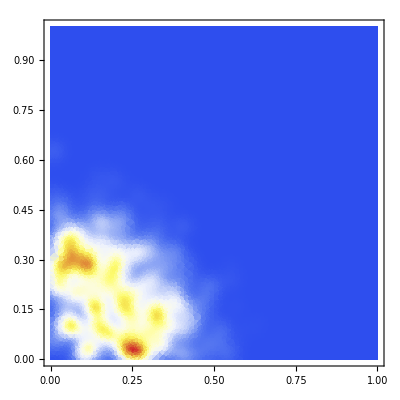

```mathematica
SmoothDensityHistogram[samples[[All,1;;2]],PlotRange->{{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

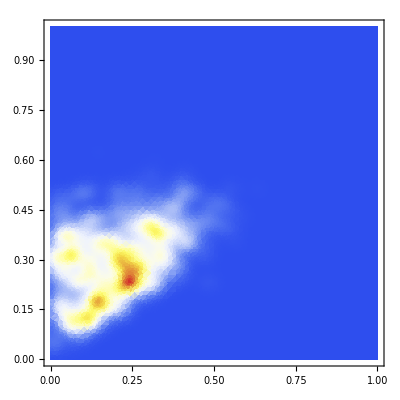

```mathematica
SmoothDensityHistogram[samples[[All,{1,3}]],PlotRange->{{0,1},{0,1}},ColorFunction->"TemperatureMap"]
```

```mathematica
sampleQ=fQ@@@samples;
```

```mathematica
{Mean[sampleQ[[All,1]]],Variance@sampleQ[[All,1]]}
```

{0.202084,0.0135715}

```mathematica
{Mean[sampleQ[[All,2]]],Variance@sampleQ[[All,2]]}
```

{0.813555,0.0113417}

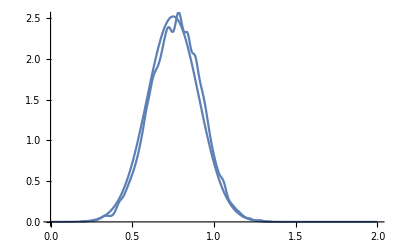

```mathematica
Show[Plot[PDF[NormalDistribution[0.75,Sqrt@0.025],x],{x,0,2}],SmoothHistogram[sampleQ[[All,1]]]]
```

## Trying X ~ N(μ,0.1) model again, where X ~ N(0,1)

```mathematica
Integrate[PDF[NormalDistribution[0,1],d] PDF[NormalDistribution[μ,0.5],d],{d,-∞,∞}]
```

0.356825 ⅇ^(-0.4 μ^2)

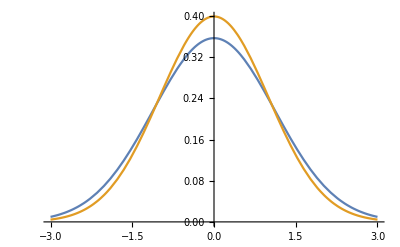

```mathematica
Plot[{0.35682482323055426 ⅇ^(-0.40000000000000036 μ^2),0.3989422804012336 ⅇ^(-0.4996337890625 μ^2)},{μ,-3,3}]
```

```mathematica
s
```

```mathematica
PDF[NormalDistribution[μ,0.1],d]
```

```mathematica
1/(2(1+0.1^2))
```

0.49505

```mathematica
N@PDF[NormalDistribution[0,Sqrt[99/100]],μ]
```

0.400952 2.71828^(-0.505051 μ^2)

```mathematica
1/Sqrt[1/1.1]
```

1.04881

```mathematica
PDF[NormalDistribution[μ,0.1],d]
```

3.98942 ⅇ^(-50. (d-μ)^2)

```mathematica
PDF[NormalDistribution[0,1],d]
```

(ⅇ^(-d^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[0,Sqrt[99/100]],μ]PDF[NormalDistribution[μ,0.1],d],{μ,-∞,∞}]
```

0.398942 ⅇ^(-0.5 d^2)

```mathematica
Integrate[0.39696240574660724 ⅇ^(-0.49504950495051503 μ^2)PDF[NormalDistribution[μ,0.1],d],{μ,-50,50}]
```

ⅇ^(-0.490196 d^2) (0.197506 Erf[355.299-7.03632 d]+0.197506 Erf[355.299+7.03632 d])

```mathematica
Integrate[PDF[NormalDistribution[0,Sqrt[99/100]],μ]PDF[NormalDistribution[μ,0.1],d],{μ,-50,50}]
```

ⅇ^(-0.5 d^2) (0.199471 Erf[355.335-7.03562 d]+0.199471 Erf[355.335+7.03562 d])

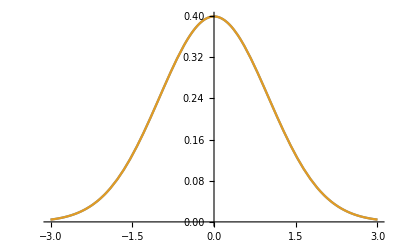

```mathematica
Plot[{PDF[NormalDistribution[0,1],d],ⅇ^(-0.4999999999999929 d^2) (0.19947114020071635 Erf[355.33452725935075-7.035623639735144 d]+0.19947114020071635 Erf[355.33452725935075+7.035623639735144 d])},{d,-3,3}]
```

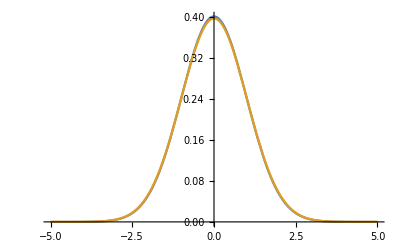

```mathematica
Plot[{PDF[NormalDistribution[0,Sqrt[99/100]],μ],0.39696240574660724 ⅇ^(-0.49504950495051503 μ^2)},{μ,-5,5}]
```

## Logistic model